### Обработка результатов измерений лабораторной работы №19 “ОПРЕДЕЛЕНИЕ УГЛОВОГО КОЭФФИЦИЕНТА ИЗЛУЧЕНИЯ МЕТОДОМ СВЕТОВОГО МОДЕЛИРОВАНИЯ” Режим 1: Входные данные: I13(mA), I0(mA),x(mm)

```mathematica
I13atModeOne={0.46,3.05,17.04,22.92,23.36,23.18,18.73,3.78,0.37,0.15,1.31,13.06,20.23,21.28,21.20,20.15,14.11,3.55,0.79,0.67,3.09,14.22,20.58,21.81,21.07,7.17};
I0listAtModeOne={24.74,23.3,24.06};
x=Range[0,125,5];
x1=First[x];x2=Last[x];
```

#### Среднеарифметическое значение тока фотодиода: (mA)

```mathematica
I0meanAtModeOne=Mean[I0listAtModeOne]
```

24.0333

#### Средние угловые коэффициенты излучения: x1- координата старта измерений(mm) x2- координата конца измерений(mm) φMean1to2-средний угловой коэффициент ( от 1 к 2) φMean1to3-средний угловой коэффициент ( от 1 к 3) -Graphics- Интеграл в числителе находим численно:

```mathematica
FunctionInNumeratorIntegralAtModeOne=Interpolation[Transpose[{x,I13atModeOne}]];
NumeratorAtModeOne=NIntegrate[FunctionInNumeratorIntegralAtModeOne[x],{x,0,125}]
```

1573.08

```mathematica
φ13AtModeOne=NumeratorAtModeOne/(I0meanAtModeOne*(x2-x1))
```

0.523632

```mathematica
φ12AtModeOne=1-φ13AtModeOne
```

0.476368

#### Режим 2:

```mathematica
I13atModeTwo={0.52,3.95,19.03,25.0,25.74,25.25,19.68,3.11,0.22,0.13,1.54,14.59,22.78,23.92,23.89,22.47,14.27,2.82,0.85,0.84,5.48,18.09,24.3,24.91,23.15,8.04};
I0listAtModeTwo={27.5,26.02,26.72};
```

```mathematica
I0meanAtModeTwo=Mean[I0listAtModeTwo]
```

26.7467

```mathematica
FunctionInNumeratorIntegralAtModeTwo=Interpolation[Transpose[{x,I13atModeTwo}]];
NumeratorAtModeTwo=NIntegrate[FunctionInNumeratorIntegralAtModeTwo[x],{x,0,125}]
```

1757.49

```mathematica
φ13AtModeTwo=NumeratorAtModeTwo/(I0meanAtModeTwo*(x2-x1))
```

0.52567

```mathematica
φ12AtModeTwo=1-φ13AtModeTwo
```

0.47433

#### Режим 3:

```mathematica
I13atModeThree={0.42,2.70,17.47,22.10,22.58,22.12,17.67,3.16,0.15,0.16,1.84,13.64,20.01,20.88,20.78,19.55,11.56,2.22,0.86,0.92,6.08,17.13,21.12,21.69,20.97,7.44};
I0listAtModeThree={23.67,22.09,22.99};
I0meanAtModeThree=Mean[I0listAtModeThree]
```

22.9167

```mathematica
FunctionInNumeratorIntegralAtModeThree=Interpolation[Transpose[{x,I13atModeThree}]];
NumeratorAtModeThree=NIntegrate[FunctionInNumeratorIntegralAtModeThree[x],{x,0,125}]
```

1560.79

```mathematica
φ13AtModeThree=NumeratorAtModeThree/(I0meanAtModeThree*(x2-x1))
```

0.544857

```mathematica
φ12AtModeThree=1-φ13AtModeThree
```

0.455143

#### Изобразим графики подынтегральных функций из числителя формулы φ13:

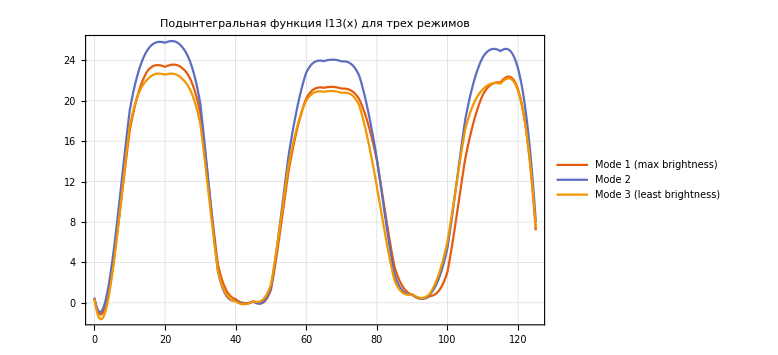

```mathematica
Plot[{FunctionInNumeratorIntegralAtModeOne[x],FunctionInNumeratorIntegralAtModeTwo[x],FunctionInNumeratorIntegralAtModeThree[x]},{x,x1,x2},PlotLabel->"Подынтегральная функция I13(x) для трех режимов",PlotTheme->"Scientific",PlotLegends->{"Mode 1 (max brightness)","Mode 2","Mode 3 (least brightness)"},ImageSize->Large,GridLines->Automatic]
```

#### Теоретическое значение средних угловых коэффициентов излучения: -Graphics-,где d-наружный диаметр труб(mm), а s-шаг между трубами(mm)

```mathematica
d=20.;s=45.; φ13Theoretical=d/s*(√((s/d)^2-1)-ArcCos[d/s])
```

0.402365

```mathematica
φ12Theoretical=1- φ13Theoretical
```

0.597635

#### Погрешности(δφ13,δφ12)

```mathematica
φ13ExperimentalMean=Mean[{φ13AtModeOne,φ13AtModeTwo,φ13AtModeThree}]
```

0.531387

```mathematica
δφ13=Abs[φ13Theoretical-φ13ExperimentalMean]/φ13Theoretical
```

0.320657

```mathematica
φ12ExperimentalMean=Mean[{φ12AtModeOne,φ12AtModeTwo,φ12AtModeThree}]
```

0.468613

```mathematica
δφ12=Abs[φ12Theoretical-φ12ExperimentalMean]/φ12Theoretical
```

0.215887